The Chebyshev-Gauss-Lobatto nodes are set up below for n=128 points and stored in variable X.

```mathematica
a = -1;
b = 1;
n = 128;
X = N[Table[(a+b)/2+(a-b)/2 Cos[(i π)/n],{i,0,n}]];
```

The Chebyshev differentiation matrices  are constructed using the following commands.

```mathematica
D1=NDSolve`FiniteDifferenceDerivative[Derivative[1],X,"DifferenceOrder"->"Pseudospectral"]@"DifferentiationMatrix";
D2=NDSolve`FiniteDifferenceDerivative[Derivative[2],X,"DifferenceOrder"->"Pseudospectral"]@"DifferentiationMatrix";
```

Considering the function f[x_] := ⅇ^(-x^2):

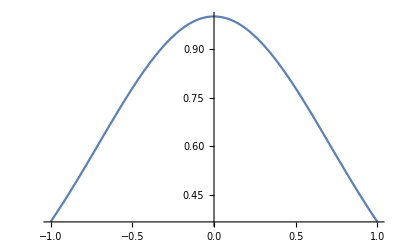

```mathematica
f[x_] := ⅇ^(-x^2)
Plot[f[x],{x,a,b}]
fpExact = f'[X];
fpNumerical = D1. f[X];
```

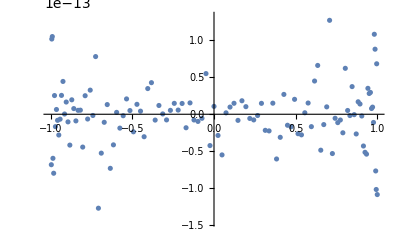

```mathematica
fpExact = f'[X];
fpNumerical = D1. f[X];
fpError = fpNumerical-fpExact;
ListPlot[Transpose[{X,fpError}]]
(*The graph shows the difference between the numerically and analytically evaluated derivative of f *)
```

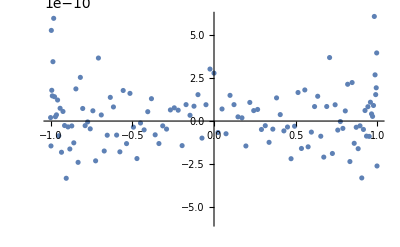

```mathematica
f2pExact = f''[X];
f2pNumerical = D2. f[X];
f2pError = f2pNumerical-f2pExact;
ListPlot[Transpose[{X,f2pError}]]
```

It can be seen that the first order pseudo spectral method is accurate approximately to order 1 x10^-13 and the second order method is accurate to order 1 x10^-10.

Q2) The harmonic oscillator system is written below in the form  du/dt=f(t,u)  where u is a vector equal to {x_,y_,Px_,Py_} :

```mathematica
F[t_,{x_,y_,Px_,Py_}]={Px,Py,-x-2y(Py/Px),-x(Px/Py)-2y}; 
F[t_,{x_,y_,Px_,Py_}]={Px,Py,-x,-2y}; 
h=0.1;
T = Range[0,100,h];
U = ConstantArray[{0,0,1,1},Length[T]];
V[x_,y_] = 1/2(x^2+2 y^2);
```

The RK2 method is implemented below to solve for u.

```mathematica
Do[K1=h*F[T[[i]],U[[i]]];   (*dU/dt*)
K2=h*F[T[[i]]+h/2,U[[i]]+K1/2];
U[[i+1]]=U[[i]]+K2,
{i,1,Length[T]-1}]
```

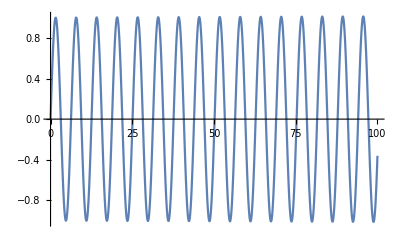

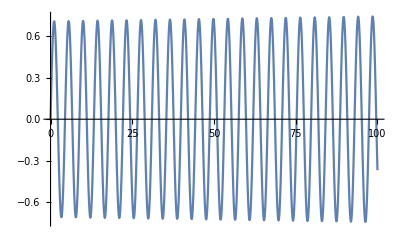

```mathematica
xList = U[[All,1]];
yList = U[[All,2]];
ListPlot[Transpose[{T,xList}],Joined->True]
ListPlot[Transpose[{T,yList}],Joined->True]
```

The energy (1/2(p_x^2+p_y^2) + V[x,y]) is calculated and plotted below.

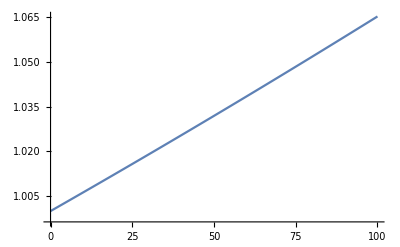

```mathematica
PxList = U[[All,3]];
PyList = U[[All,4]];
V[xList,yList];
Energy = 1/2(PxList^2+PyList^2)+V[xList,yList];
ListPlot[Transpose[{T,Energy}],Joined->True]
```

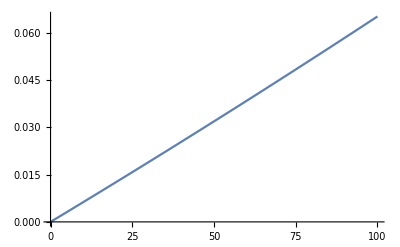

```mathematica
dE = (1/2(PxList^2+PyList^2)+V[xList,yList])-Energy[[1]];
dE[[174]];
ListPlot[Transpose[{T,dE}],Joined->True]
(*Plot of the difference between energy at each time step and the intial energy*)
```

It can be seen that using the RK2 method, energy is not conserved as the energy is linearly increasing with time. This is due to the implementation of a second order method rather than a higher order method.

```mathematica
(*Trapezium rule implementation*)
Uold = ConstantArray[{0,0,1,1},Length[T]];
Unew = ConstantArray[{0,0,1,1},Length[T]];
Do[K1=h*F[T[[i]],Uold[[i]]];   (*dU/dt*)
K2=h*F[T[[i]]+h/2,Uold[[i]]+K1/2];
Uold[[i+1]]=Uold[[i]]+K2;
Unew[[i+1]] = Uold[[i+1]];
Do[Unew[[i+1]]= Unew[[i]] + h/2 +F[T[[i+1]],Unew[[i+1]]]+F[T[[i]],Unew[[i]]],
{j,1,10}],
{i,1,Length[T]-1}]
```

```mathematica
Utrap = ConstantArray[{0,0,1,1},Length[T]];

Do[K1=h*F[T[[i]],Utrap[[i]]];   (*dU/dt*)
K2=h*F[T[[i]]+h/2,Utrap[[i]]+K1/2];
Utrap[[i+1]]=Utrap[[i]]+K2;
Do[Utrap[[i+1]]= Utrap[[i]] + h/2 (F[T[[i+1]],Utrap[[i+1]]]+F[T[[i]],Utrap[[i]]]),
{j,1,10}],
{i,1,Length[T]-1}]
```

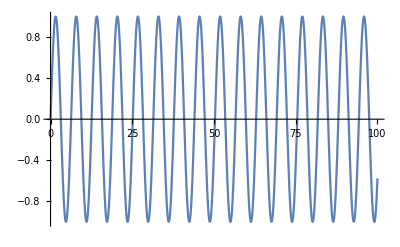

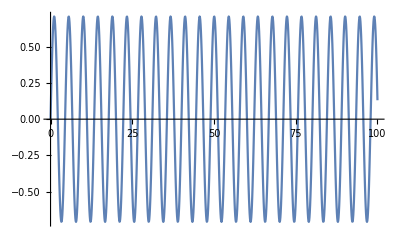

```mathematica
Utrap;
ListPlot[Transpose[{T,Utrap[[All,1]]}],Joined->True] (*x*)
ListPlot[Transpose[{T,Utrap[[All,2]]}],Joined->True](*y*)
```

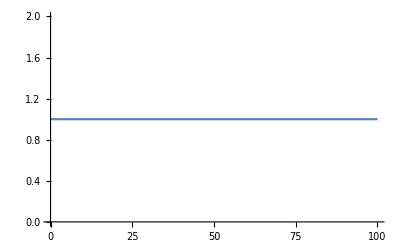

```mathematica
EnergyTrap = 1/2(Utrap[[All,3]]^2+Utrap[[All,4]]^2)+V[Utrap[[All,1]],Utrap[[All,2]]];
ListPlot[Transpose[{T,EnergyTrap}],Joined->True]
```

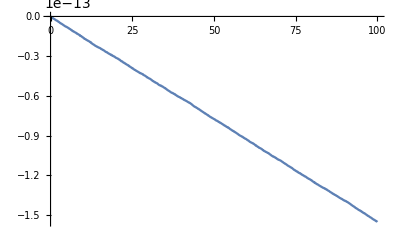

```mathematica
dETrap = EnergyTrap-EnergyTrap[[1]];
ListPlot[Transpose[{T,dETrap}],Joined->True]
```

The two graphs above show that energy is conserved to order 1x10^-13, a large improvement on the second order Runge Kutta method.

Q3)

```mathematica
u[t_,x_] = ⅇ^(-218(-2/3+t-Log[1-x])^2);
D[u[t,x], t]-(1-x)D[u[t,x], x]
```

0

Therefore u = ⅇ^(-218( -2/3+t-Log[1-x])^2) satisfies the hyperboloidal advection equation.

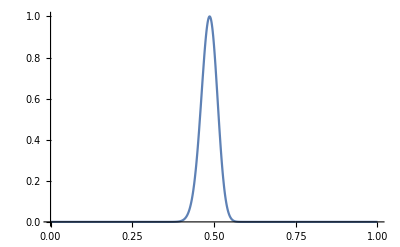

```mathematica
(*Plotting the initial data - If statements used to avoid underflow errors*)
f[x_]  = If[x>0.75,0.,ⅇ^(-218( -2/3-Log[1-x])^2)];
SetAttributes[f,Listable]
a=0;
b=1;

Plot[f[x],{x,a,b},PlotRange->All]
```

```mathematica
(*Pseudospectral gridpoints*)
n1=255;
Θ=Subdivide[0,π,n1]//N;
Z=-Cos[Θ];
X=(a+b)/2+(b-a)/2 Z ;   (*Chebyshev-Gauss-Lobatto nodes*)
Δx=X[[2]]-X[[1]];    (*minimum grid spacing*)

D1=NDSolve`FiniteDifferenceDerivative[Derivative[1],X,"DifferenceOrder"->"Pseudospectral",PeriodicInterpolation->False]@"DifferentiationMatrix";
D1=Developer`ToPackedArray[D1,Real];
```

Since ∂_t u=(1-x)∂_x u ,  
∂_t u=F(t,u) u where F[t,u] =(1-x)∂_x = (1-x)D1 by the method of lines.

```mathematica
F[t_,u_]:=(1-X)D1.u (*dU/dt=F(t,U)=-D1.U *)
```

```mathematica
m1=100000; 
tend=1;
Δt=(b-a)/m1;(*tend/m1;*)
T=Subdivide[0.,tend,m1]//N;
U=.
U=ConstantArray[0.,{m1+1,n1+1}];     
U=Developer`ToPackedArray[U,Real];
(*fX = Developer`ToPackedArray[f[X],Real];*)
U[[1,All]]=f[X];
Developer`PackedArrayQ[U];
```

```mathematica
Δt/Δx (* Courant Limit : C ∝ Δt/Δx*)
```

0.26354

Using time-step yields a Δt/Δx=0.26<1 which is good for stability purposes. Once the Δt/Δxvalue begins to exceed 1, instability arises as the system evolves through time.

```mathematica
(*RK4 method*)
Do[K1=Δt*F[T[[ν]],U[[ν]]];   (*dU/dt=F(t,U)*)
K2=Δt*F[T[[ν]]+Δt/2,U[[ν]]+K1/2];
K3=Δt*F[T[[ν]]+Δt/2,U[[ν]]+K2/2];
K4=Δt*F[T[[ν]]+Δt,U[[ν]]+K3];
U[[ν+1]]=U[[ν]]+(K1+2K2+2K3+K4)/6,
{ν,1,m1}]
```

```mathematica
Manipulate[ListPlot[Transpose[{X,U[[ν]]}],PlotRange->All],{ν,1,m1+1}]
Manipulate[ListPlot[Transpose[{X,U[[ν]]-f[X+T[[ν]]]}],PlotRange->All],{ν,1,m1+1}]
```

Part::partd: Part specification U⟦15800.⟧ is longer than depth of object.

Part::partd: Part specification U⟦8200.⟧ is longer than depth of object.

Part::partd: Part specification U⟦1.⟧ is longer than depth of object.

Part::partd: Part specification T⟦1.⟧ is longer than depth of object.

Part::partd: Part specification U⟦1.⟧ is longer than depth of object.

```mathematica
(*Clenshaw-Curtis quadrature weights for integration*)
n=n1;
If[Mod[n,2]==0,W=2/n(1-Cos[n Θ]/(n^2-1)-∑_(k=1)^(n/2-1) (2Cos[2k Θ])/(4 k^2-1));
W[[1]]=1./(n^2-1);W[[-1]]=W[[1]];,
W=2/n(1-∑_(k=1)^((n-1)/2) (2Cos[2k Θ])/(4 k^2-1));W[[1]]=1./n^2;W[[-1]]=W[[1]];]
W=W*(b-a)/2;
```

The energy is calculated and plotted below using the Clenshaw Curtis weights.

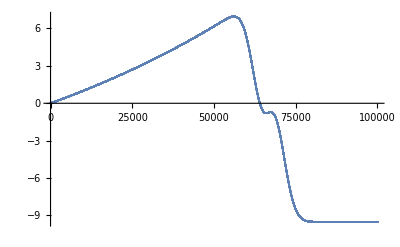

```mathematica
energy = ConstantArray[0.,{m1}];
Do[energy[[it]]=W.((1-X)D1.U[[it,All]])^2, {it,1,m1}]
ListPlot[energy-energy[[1]]]
```

A implicit Hermite method is now implemented below and a graph of the solution obtained is displayed:

```mathematica
(*Implicit Method - using Hermite method*)
(II=IdentityMatrix[n1+1]//N);
L=(1-X)D1;
L2 = L.L;
L3 = L2.L;
m1= 100000;
Δt= (b-a)/m1;
U=.
U=ConstantArray[0.,{m1+1,n1+1}];     
U=Developer`ToPackedArray[U,Real];
U[[1,All]]=f[X];
M=.
(*M= (II+Δt L + Δt^2/2 L2 +Δt^2/6 L3); (*RK3*)*)

M= Inverse[(II-Δt/2 L+Δt^2/12 L2)].(II+Δt/2 L+Δt^2/12 L2);(*Hermite*)
```

```mathematica
Do[U[[it+1,All]]=M.U[[it,All]],{it,1,m1}]
Manipulate[ListPlot[Transpose[{X,U[[ν]]}],PlotRange->All],{ν,1,m1+1}]
```

Q4)

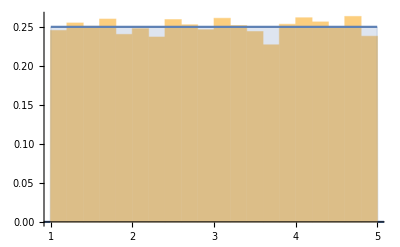

```mathematica
u = RandomReal[{1,5},15000];
Histogram[u,Automatic,"PDF"];
Plot[PDF[UniformDistribution[{1,5}],x],{x,0,10},Filling->Bottom];
Show[%%,%] (*Uniform distribution over interval [1,5]*)
```

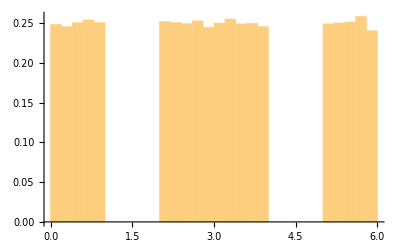

```mathematica
i1 = RandomReal[{0,1},15000];
i2 = RandomReal[{2,3},15000];
i3 = RandomReal[{3,4},15000];
i4 = RandomReal[{5,6},15000];
(*Uniform distribution over union of intervals [0,1],[2,4],[5,6]*)
Histogram[Union[i1,i2,i3,i4],Automatic,"PDF"]
```

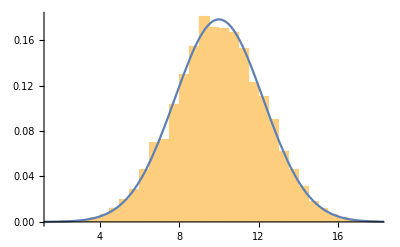

```mathematica
u1=.
u2=.
x=.
y=.
u1=ConstantArray[0.,10000];
u2=ConstantArray[0.,10000];
x=ConstantArray[0.,10000];
y=ConstantArray[0.,10000];
Do[u1[[i]]=RandomReal[];
u2[[i]]=RandomReal[];
r=Sqrt[-2*Log[u1[[i]]]];
v=2*Pi*u2[[i]];
x[[i]]=r*Cos[v];
y[[i]]=r*Sin[v],{i,1,10000}]
Histogram[(x*Sqrt[5])+10,Automatic,"PDF"];
Histogram[(y*Sqrt[5])+10,Automatic,"PDF"];
Plot[PDF[NormalDistribution[10,√5],x],{x,0,20}];
Show[%%,%] (*Gaussian mean=10, variance = 5*)
```

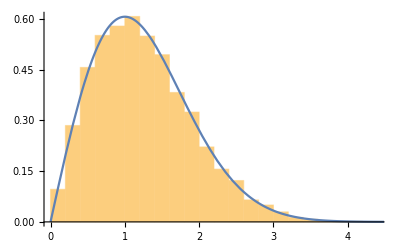

```mathematica
x=.
f[x_,λ_] =x/λ^2  ⅇ^(-x^2/(2 λ^2));
∫_0^x f[x,λ]ⅆx;
Solve[1-ⅇ^(-x^2/(2 λ^2))==y,x];
u=RandomReal[{0,1},15000];
λ=1;
x = √2 λ √(-Log[1-u])   ;
Histogram[x,Automatic,"PDF"];
Plot[PDF[RayleighDistribution[λ],x],{x,0,5}];
Show[%%,%]
```

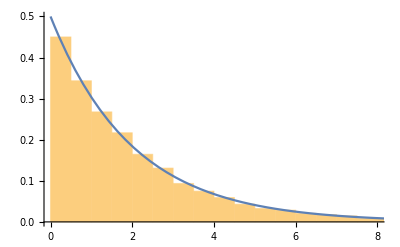

```mathematica
x=.
u=RandomReal[{0,1},15000];
x = -2Log[1-u] ;
Histogram[x,Automatic,"PDF"];
Plot[PDF[ChiSquareDistribution[2],x],{x,0,10}];
Show[%%,%]
```

Q5)

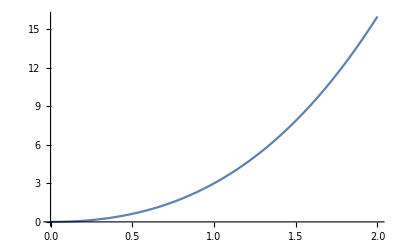

```mathematica
f[x_] = x^3+2 x^2;
Plot[f[x],{x,0,2}]
```

```mathematica
Iexact =∫_0^2 f[x]ⅆx //N
```

9.33333

A hit and miss Monte Carlo method is implemented in order to obtain an estimate for the integral above.

```mathematica
hitmiss[n0_]:=Module[{n=n0},(*The area of the sample space is equal to 3*)A=32;
(*sample n abscissas uniformly in[0,3]*)X=RandomReal[{0,2},n];
(*sample n ordinates uniformly in[0,1]*)Y=RandomReal[{0,16},n];
(*Count only those points with y<f(x)*)k=Count[UnitStep[Y-f[X]],0];
(*Get the "Hit-miss" Monte Carlo estimate:*)II=A*k/n]
```

```mathematica
MCIs = ConstantArray[0,6]; (*Code was taking far too long to include more points*)
Do[MCIs[[j]]=hitmiss[10^j],{j,1,6}]
```

```mathematica
MCIs//N
```

{16.,13.12,9.056,9.1552,9.2528,9.32368}

```mathematica
Errors = Abs[MCIs- Iexact]
```

{6.66667,3.78667,0.277333,0.178133,0.0805333,0.00965333}

It can be seen that the Monte Carlo Integration estimates are approaching the true value (9.3333) and the errors are decreasing as the number of samples increases.

```mathematica
hitmissvar[n0_]:=Module[{n=n0},(*The area of the sample space is equal to 3*)A=32;
(*sample n abscissas uniformly in[0,3]*)X=RandomReal[{0,2},n];
(*sample n ordinates uniformly in[0,1]*)Y=RandomReal[{0,16},n];
(*Count only those points with y<f(x)*)k=Count[UnitStep[Y-f[X]],0];
(*Get the "Hit-miss" Monte Carlo estimate:*)s = Sqrt[II(A-II)/n]]
```

```mathematica
MCIvars = ConstantArray[0,15]; (*Code was taking far too long to include more points*)
Do[MCIvars[[j]]=hitmissvar[2^j],{j,1,15}]
```

```mathematica
MCIvars//N
```

{10.2817,7.27026,5.14085,3.63513,2.57043,1.81757,1.28521,0.908783,0.642606,0.454391,0.321303,0.227196,0.160652,0.113598,0.0803258}

It can be seen that the variance of the Monte Carlo integration estimates are decreasing as the sample size increases with the lowest variance (0.08035) being produced with the largest sample of 2^15

Q6)

```mathematica
Subscript[ψ, analytical][t_,x_] = ⅇ^(-218( -2/3+t-Log[1-x])^2);
(* -(1+x)(∂_t)^2 Subscript[ψ, analytical][t,x]+(1-2 x^2)∂_t ∂_x Subscript[ψ, analytical][t,x]+(1-x)x^2(∂_x)^2 Subscript[ψ, analytical][t,x]-2x∂_t Subscript[ψ, analytical][t,x]+x(2-3x)∂_x Subscript[ψ, analytical][t,x]==0 *)
-(1+x)D[Subscript[ψ, analytical][t,x], {t,2}]+(1-2 x^2)D[D[Subscript[ψ, analytical][t,x], t], x]+(1-x)x^2 D[Subscript[ψ, analytical][t,x], {x,2}]-2x D[Subscript[ψ, analytical][t,x], t]+x(2-3x)D[Subscript[ψ, analytical][t,x], x]//Simplify
```

0

Therefore ψ_(analytical =)ⅇ^(-218( -2/3+t-Log[1-x])^2) satisfies the hyperboloidal wave equation.

Substituting the auxiliary variable  π == ∂_t ψ into the hyperboloidal wave equation, the following  equation is obtained:
(1+x)∂_t π=(1-2 x^2)∂_x π+(1-x)x^2(∂_x)^2 ψ-2xπ+x(2-3x)∂_x ψ
⇒ ∂_t π = (((1-x)x^2(∂_x)^2+x(2-3x)∂_x)/(1+x))ψ+(((1-2 x^2)∂_x -2x)/(1+x))π

Reducing the wave equation to a system of first order in time, of the form   ∂_t u=L u, where u=(ψ
π)  and   L = (0 | 1
L_1 | L_2):
∂_t (ψ
π) =(0 | 1
L_1 | L_2)(ψ
π)=(0 | 1
(((1-x)x^2(∂_x)^2+x(2-3x)∂_x)/(1+x)) | (((1-2 x^2)∂_x -2x)/(1+x)))(ψ
π)

Therefore  L_(2N x 2N)=(0_NxN | I_NxN
(((1-x)x^2 D2+x(2-3x)D1)/(1+x))_NxN | (((1-2 x^2)D1-2x)/(1+x))_NxN) by the method of lines.

-Graphics-

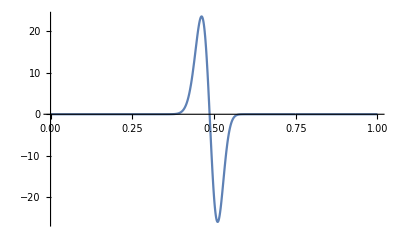

```mathematica
(*Plotting the initial data - If statements used to avoid underflow errors*)
f[x_]  = If[x>0.75,0.,ⅇ^(-218( -2/3-Log[1-x])^2)];
df[x_] = If[x>0.75,0.,-(436 ⅇ^(-218 (-2/3-Log[1-x])^2) (-2/3-Log[1-x]))/(1-x)];
SetAttributes[f,Listable]
SetAttributes[df,Listable]

a=0;
b=1;

Plot[f[x],{x,a,b},PlotRange->All]
Plot[df[x],{x,a,b},PlotRange->All]
```

```mathematica
(*Pseudospectral gridpoints*)
n1=255;
Θ=Subdivide[0,π,n1]//N;
Z=-Cos[Θ];
X=(a+b)/2+(b-a)/2 Z ;   (*Chebyshev-Gauss-Lobatto nodes*)
Δx=X[[2]]-X[[1]];    (*minimum grid spacing*)

D1=NDSolve`FiniteDifferenceDerivative[Derivative[1],X,"DifferenceOrder"->"Pseudospectral",PeriodicInterpolation->False]@"DifferentiationMatrix";
D2=NDSolve`FiniteDifferenceDerivative[Derivative[2],X,"DifferenceOrder"->"Pseudospectral",PeriodicInterpolation->False]@"DifferentiationMatrix";
D1=Developer`ToPackedArray[N[Normal[D1]],Real];
D2=Developer`ToPackedArray[N[Normal[D2]],Real];
```

```mathematica
(ONN=ConstantArray[0.,{n1+1,n1+1}]);
(INN=IdentityMatrix[n1+1]//N);
L1 = ((1-X)X^2 D2+X(2-3X)D1)/(1+X);
L2 = ((1-2 X^2)D1-2X)/(1+X);
L2N2N=ArrayFlatten[{{ONN,INN},{L1,L2}}];
ByteCount[L2N2N];
L1=Developer`ToPackedArray[L1,Real];
Developer`PackedArrayQ[L2N2N];
ByteCount[L2N2N];
F[t_,u_]:=L2N2N.u (*dU/dt=F(t,U)=L.U *)
```

```mathematica
m1=100000; 
tend=10;
Δt= (b-a)/m1;(*tend/m1;*)
T=Subdivide[0.,tend,m1]//N;
(*T=Developer`ToPackedArray[T,Real];*)
U=.
U=ConstantArray[0.,{m1+1,2n1+2}];      
U=Developer`ToPackedArray[U,Real];
 (*Initial conditions  Subscript[U0, i]=U(t0,Subscript[x, i]), Subscript[U, i]^ν=U(Subscript[t, ν],Subscript[x, i])*)
FX=Developer`ToPackedArray[f[X],Real];
mdFdX=Developer`ToPackedArray[(1-X)*df[X],Real];
U[[1,1;;n1+1]]=FX;
U[[1,n1+2;;-1]]=mdFdX;
ByteCount[U];
Developer`PackedArrayQ[U];
```

```mathematica
(*RK4 method implementation*)
Do[K1=Δt*F[T[[ν]],U[[ν]]];   (*dU/dt=F(t,U)*)
K2=Δt*F[T[[ν]]+Δt/2,U[[ν]]+K1/2];
K3=Δt*F[T[[ν]]+Δt/2,U[[ν]]+K2/2];
K4=Δt*F[T[[ν]]+Δt,U[[ν]]+K3];
U[[ν+1]]=U[[ν]]+(K1+2K2+2K3+K4)/6,
{ν,1,m1}]
```

```mathematica
ψ=U[[All,1;;n1+1]];       (*Subscript[ψ, i]^ν=ψ(Subscript[t, ν],Subscript[x, i])*)
p=U[[All,n1+2;;-1]];
```

```mathematica
Manipulate[ListPlot[Transpose[{X,f[X+T[[ν]]]}],PlotRange->All,Joined->True,InterpolationOrder->3],{ν,1,m1+1}];
Manipulate[ListPlot[Transpose[{X,ψ[[ν]]}],PlotRange->All],{ν,1,m1+1}]
```

It can be seen that using the above RK4 implementation produces an accurate solution, however as the time increases instability can be seen.
Once the Courant Limit has been exceeded, the analytical solutions errors becomes extremely large as the time increases.

E = ∫_0^1 (1+x)p^2+x^2(1-x)(D1.ψ)^2 ⅆx

```mathematica
(*Clenshaw-Curtis quadrature weights for integration*)
n=n1;
If[Mod[n,2]==0,W=2/n(1-Cos[n Θ]/(n^2-1)-∑_(k=1)^(n/2-1) (2Cos[2k Θ])/(4 k^2-1));
W[[1]]=1./(n^2-1);W[[-1]]=W[[1]];,
W=2/n(1-∑_(k=1)^((n-1)/2) (2Cos[2k Θ])/(4 k^2-1));W[[1]]=1./n^2;W[[-1]]=W[[1]];]
W=W*(b-a)/2;

energy = ConstantArray[0.,{m1}]
Do[energy[[it]]=W.((p^2).(1+X)+(ψ^2).(X^2(1-X).D2))^2,{it,1,m1}]
Dimensions[(p^2).(1+X)+(ψ^2).(X^2(1-X).D2)]
```

If[Mod[n1,2]==0,W=(2 (1-Cos[n Θ]/(n^2-1)-∑_(k=1)^(n/2-1) (2 Cos[2 k Θ])/(4 k^2-1)))/n;W⟦1⟧=1./(n^2-1);W⟦-1⟧=W⟦1⟧;,W=(2 (1-∑_(k=1)^((n-1)/2) (2 Cos[2 k Θ])/(4 k^2-1)))/n;W⟦1⟧=1./n^2;W⟦-1⟧=W⟦1⟧;]

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -a+b.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0.,{m1}].

ConstantArray[0.,{m1}]

Do::iterb: Iterator {it,1,m1} does not have appropriate bounds.

Do[energy⟦it⟧=W.(p^2.(1+X)+ψ^2.(X^2 (1-X).D2))^2,{it,1,m1}]

{2}

```mathematica
Dimensions[((p^2).(1+X))+((ψ^2).(X^2(1-X).D2))]
Dimensions[(p^2).(1+X)]
```

{2}

{2}

```mathematica
X^2(1-X)
```

{0.,1.43976×10^-9,2.30319×10^-8,1.16562×10^-7,3.6823×10^-7,8.98488×10^-7,1.86181×10^-6,3.44639×10^-6,5.87382×10^-6,9.3986×10^-6,0.0000143077,0.0000209201,0.000029586,0.0000406862,0.0000546315,0.0000718618,0.0000928453,0.000118077,0.00014808,0.000183401,0.000224612,0.000272308,0.000327106,0.000389644,0.000460579,0.000540588,0.000630363,0.000730614,0.000842063,0.000965446,0.00110151,0.00125101,0.00141471,0.00159339,0.00178782,0.00199878,0.00222706,0.00247344,0.00273869,0.0030236,0.00332894,0.00365549,0.00400399,0.0043752,0.00476985,0.00518868,0.00563239,0.00610169,0.00659723,0.00711969,0.0076697,0.00824788,0.0088548,0.00949104,0.0101571,0.0108536,0.0115809,0.0123395,0.0131297,0.0139521,0.0148069,0.0156944,0.0166149,0.0175686,0.0185558,0.0195765,0.0206309,0.021719,0.0228409,0.0239966,0.0251859,0.0264087,0.027665,0.0289545,0.0302768,0.0316318,0.0330191,0.0344383,0.0358889,0.0373704,0.0388823,0.040424,0.0419948,0.0435941,0.0452211,0.046875,0.048555,0.0502602,0.0519896,0.0537424,0.0555174,0.0573137,0.05913,0.0609653,0.0628183,0.0646878,0.0665726,0.0684713,0.0703825,0.072305,0.0742372,0.0761777,0.078125,0.0800776,0.082034,0.0839926,0.0859517,0.0879098,0.0898652,0.0918163,0.0937613,0.0956986,0.0976265,0.0995432,0.101447,0.103336,0.105209,0.107063,0.108898,0.110711,0.1125,0.114265,0.116002,0.117711,0.119389,0.121036,0.122648,0.124225,0.125765,0.127266,0.128727,0.130146,0.131521,0.132852,0.134135,0.135371,0.136558,0.137693,0.138776,0.139806,0.140782,0.141701,0.142563,0.143367,0.144112,0.144797,0.14542,0.145981,0.14648,0.146914,0.147285,0.14759,0.147829,0.148002,0.148109,0.148148,0.14812,0.148024,0.14786,0.147629,0.147329,0.146961,0.146525,0.146022,0.14545,0.144812,0.144106,0.143334,0.142496,0.141593,0.140625,0.139593,0.138497,0.13734,0.136121,0.134841,0.133502,0.132105,0.13065,0.12914,0.127576,0.125959,0.124289,0.12257,0.120803,0.118988,0.117128,0.115225,0.11328,0.111296,0.109273,0.107214,0.105122,0.102997,0.100842,0.0986596,0.0964513,0.0942195,0.0919663,0.089694,0.0874048,0.085101,0.0827849,0.0804588,0.078125,0.0757859,0.073444,0.0711014,0.0687606,0.066424,0.064094,0.0617729,0.0594632,0.0571671,0.0548871,0.0526254,0.0503845,0.0481666,0.045974,0.0438091,0.0416739,0.0395709,0.037502,0.0354696,0.0334757,0.0315224,0.0296117,0.0277457,0.0259263,0.0241554,0.0224348,0.0207664,0.019152,0.0175931,0.0160916,0.0146489,0.0132665,0.011946,0.0106887,0.00949602,0.00836911,0.00730921,0.00631745,0.00539486,0.00454244,0.00376108,0.00305161,0.00241478,0.00185127,0.00136169,0.000946538,0.000606267,0.000341237,0.000151728,0.0000379421,0.}

```mathematica
(*Implicit Method - using the Hermite method*)
(II=IdentityMatrix[2n1+2]//N);
m1= 100000;
Δt= (b-a)/m1;
U=.
U=ConstantArray[0.,{m1+1,2n1+2}]; 
U[[1,1;;n1+1]]=FX;
U[[1,n1+2;;-1]]=mdFdX;     
M= Inverse[II-Δt/2 L2N2N+Δt^2/12 L2N2N.L2N2N].(II+Δt/2 L2N2N+Δt^2/12 L2N2N.L2N2N);
```

```mathematica
Do[U[[it+1,All]]=Herm.U[[it,All]],{it,1,m1}]
Manipulate[ListPlot[Transpose[{X,U[[All,1;;n1+1]][[ν]]}],PlotRange->All],{ν,1,m1+1}]
```

Part::span: 1;;1+n1 is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)